## Телица Илья Денисович гр. 221701 Вариант 12

### Задание 1

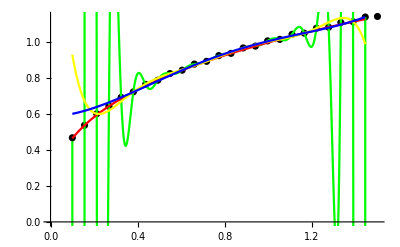

```mathematica
dataset = ({{0.1, 0.46648}, {0.156, 0.53563}, {0.212, 0.599255}, {0.268, 0.641507}, {0.324, 0.690263}, {0.38, 0.720694}, {0.436, 0.76207}, {0.492, 0.785497}, {0.548, 0.822419}, {0.604, 0.841076}, {0.66, 0.875012}, {0.716, 0.890145}, {0.772, 0.921945}, {0.828, 0.934329}, {0.884, 0.964532}, {0.94, 0.974688}, {0.996, 1.00366}, {1.052, 1.01196}, {1.108, 1.03995}, {1.164, 1.04666}, {1.22, 1.07387}, {1.276, 1.07921}, {1.332, 1.10578}, {1.388, 1.10991}, {1.444, 1.13594}, {1.5, 1.13899}});
a = 0.1;b = 1.444;total = 25;h= (b-a)/total; n1=12;n2=8;n3=5;
InterTotal[x_]=InterpolatingPolynomial[dataset,x];
InterN1[x_]=InterpolatingPolynomial[Table[dataset[[i*2]],{i,1,n1}],x];
InterN2[x_]=InterpolatingPolynomial[Table[dataset[[i*3]],{i,1,n2}],x];
InterN3[x_]=InterpolatingPolynomial[Table[dataset[[i*5]],{i,1,n3}],x];
InterTotalGraph=Plot[InterTotal[x],{x,a,b},PlotStyle->Green];
InterN1Graph=Plot[InterN1[x],{x,a,b},PlotStyle->Red];
InterN2Graph=Plot[InterN2[x],{x,a,b},PlotStyle->Yellow];
InterN3Graph=Plot[InterN3[x],{x,a,b},PlotStyle->Blue];
dotsPlot=ListPlot[dataset,PlotStyle->Black];
Show[dotsPlot,InterTotalGraph,InterN1Graph,InterN2Graph,InterN3Graph ]
```

При увеличении узлов интерполяции погрешность интерполирования уменьшается, однако в данном случае график становится менее похож на исходную функцию

### Задание 2

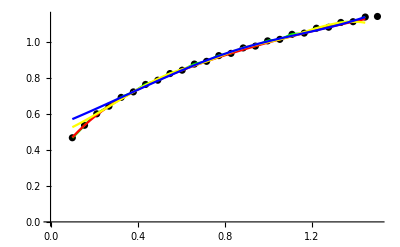

```mathematica
SplineTotal=Interpolation[dataset,Method->"Spline"];
SplineN1=Interpolation[Table[dataset[[i*2]],{i,1,n1}],Method->"Spline"];
SplineN2=Interpolation[Table[dataset[[i*3]],{i,1,n2}],Method->"Spline"];
SplineN3=Interpolation[Table[dataset[[i*5]],{i,1,n3}],Method->"Spline"];
SplineTotalGraph=Plot[SplineTotal[x],{x,a,b},PlotStyle->Green];
SplineN1Graph=Plot[SplineN1[x],{x,a,b},PlotStyle->Red];
SplineN2Graph=Plot[SplineN2[x],{x,a,b},PlotStyle->Yellow];
SplineN3Graph=Plot[SplineN3[x],{x,a,b},PlotStyle->Blue];
Show[dotsPlot,SplineTotalGraph,SplineN1Graph,SplineN2Graph,SplineN3Graph]
```

### Задание 3

Многочен 1 степени:  0.532898+0.451297 x

Многочен 2 степени:  0.425445+0.834534 x-0.248211 x^2

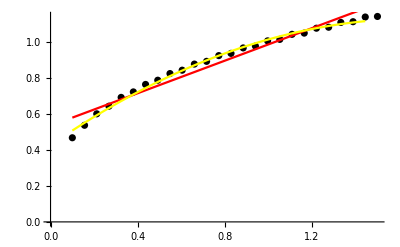

```mathematica
P1= LinearSolve[Table[Table[If[i+j==0,∑_(k=1)^total 1,∑_(k=1)^total dataset[[k,1]]^(i+j)],{i,0,1}],{j,0,1}],
Table[If[i==0,∑_(j=1)^total dataset[[j,2]],∑_(j=1)^total (dataset[[j,2]]*dataset[[j,1]]^i)],{i,0,1}]];
Pr=0;
m=1;k=0;
While[k<=m,Pr=Pr+P1[[k+1]]*x^k;k++];
Q1=Pr;
Echo[Q1,"Многочен 1 степени:"];
P2= LinearSolve[Table[Table[If[i+j==0,∑_(k=1)^total 1,∑_(k=1)^total dataset[[k,1]]^(i+j)],{i,0,2}],{j,0,2}],
Table[If[i==0,∑_(j=1)^total dataset[[j,2]],∑_(j=1)^total (dataset[[j,2]]*dataset[[j,1]]^i)],{i,0,2}]];
Pr=0;
m=2;k=0;
While[k<=m,Pr=Pr+P2[[k+1]]*x^k;k++];
Q2=Pr;
Echo[Q2,"Многочен 2 степени:"];
P1Graph=Plot[Q1,{x,a,b},PlotStyle->Red];
P2Graph=Plot[Q2,{x,a,b},PlotStyle->Yellow];
Show[dotsPlot,P1Graph,P2Graph]
```

### Задание 4

```mathematica
leftRectangleMethod[points_List]:=Module[{x,y,sum},
x=points[[All,1]];
y=points[[All,2]];
sum=Total[y[[1;;-2]]];
h*sum];
rightRectangleMethod[points_List]:=Module[{x,y,sum},
x=points[[All,1]];
y=points[[All,2]];
sum=Total[y[[2;;-1]]];
h*sum];
midRectangleMethod[points_List]:=Module[{x,y,sum},
x=points[[All,1]];
y=points[[All,2]];
sum=Total[y[[2;;-2]]];
h*sum];
trapezoidMethod[points_List]:=Module[{x,y,sum},
x=points[[All,1]];
y=points[[All,2]];
sum=Total[y[[2;;-2]]]+(y[[1]]+y[[-1]])/2;
h*sum];
simpsonMethod[points_List]:=Module[{x,y,sum},
x=points[[All,1]];
y=points[[All,2]];
sum=y[[1]]+y[[-1]]+4*Total[y[[2;;-2;;2]]]+2*Total[y[[3;;-2;;2]]];
h/3*sum];

Echo[leftRectangleMethod[dataset],"Метод левых прямоугольников"];
Echo[rightRectangleMethod[dataset],"Метод правых прямоугольников"];
Echo[midRectangleMethod[dataset],"Метод средних прямоугольников"];
Echo[trapezoidMethod[dataset],"Метод трапеций"];
Echo[simpsonMethod[dataset],"Метод Симпсона"];
```

Метод левых прямоугольников  1.18447

Метод правых прямоугольников  1.22062

Метод средних прямоугольников  1.15939

Метод трапеций  1.20254

Метод Симпсона  1.18057

Метод Симпсона считается наиболее точным, методы средних прямоугольников и трапеций схожи по точности, методы левых и правых прямоугольников являются наименее точными

### Задание 5

```mathematica
h=(b-a)/26;
firstRankDif={};
For[i=2,i<=total,i++,
firstRankDif=Append[firstRankDif,{dataset[[i,1]],(dataset[[i+1,2]]-dataset[[i-1,2]])/(2h)}];]
secondRankDif={};
For[i=2,i<=total,i++,
secondRankDif=Append[secondRankDif,{dataset[[i,1]],(dataset[[i+1,2]]-2dataset[[i,2]]+dataset[[i-1,2]])/h^2}];]

Echo[TableForm[firstRankDif],"Таблица первых производных"];
Print["  "]
Print["  "]
Print["  "]
Echo[TableForm[secondRankDif],"Таблица вторых производных"];
```

Таблица первых производных  0.156 | 1.28428
0.212 | 1.02411
0.268 | 0.880286
0.324 | 0.765946
0.38 | 0.694562
0.436 | 0.626815
0.492 | 0.583733
0.548 | 0.537594
0.604 | 0.508712
0.66 | 0.474626
0.716 | 0.453965
0.772 | 0.427375
0.828 | 0.411928
0.884 | 0.390377
0.94 | 0.37847
0.996 | 0.360518
1.052 | 0.351019
1.108 | 0.33564
1.164 | 0.328095
1.22 | 0.314844
1.276 | 0.308653
1.332 | 0.296949
1.388 | 0.291726
1.444 | 0.28128

Таблица вторых производных  0.156 | -2.06767
0.212 | -7.99859
0.268 | 2.43405
0.324 | -6.85792
0.38 | 4.09604
0.436 | -6.7172
0.492 | 5.05035
0.548 | -6.83546
0.604 | 5.71799
0.66 | -7.0368
0.716 | 6.23743
0.772 | -7.26621
0.828 | 6.66855
0.884 | -7.50235
0.94 | 7.04167
0.996 | -7.73625
1.052 | 7.36875
1.108 | -7.96379
1.164 | 7.67188
1.22 | -8.18459
1.276 | 7.94508
1.332 | -8.39791
1.388 | 8.19582
1.444 | -8.59999

Формулы дают крайне  разный результат, однако дифференцирование по формуле 2 порядка имеет большую точность